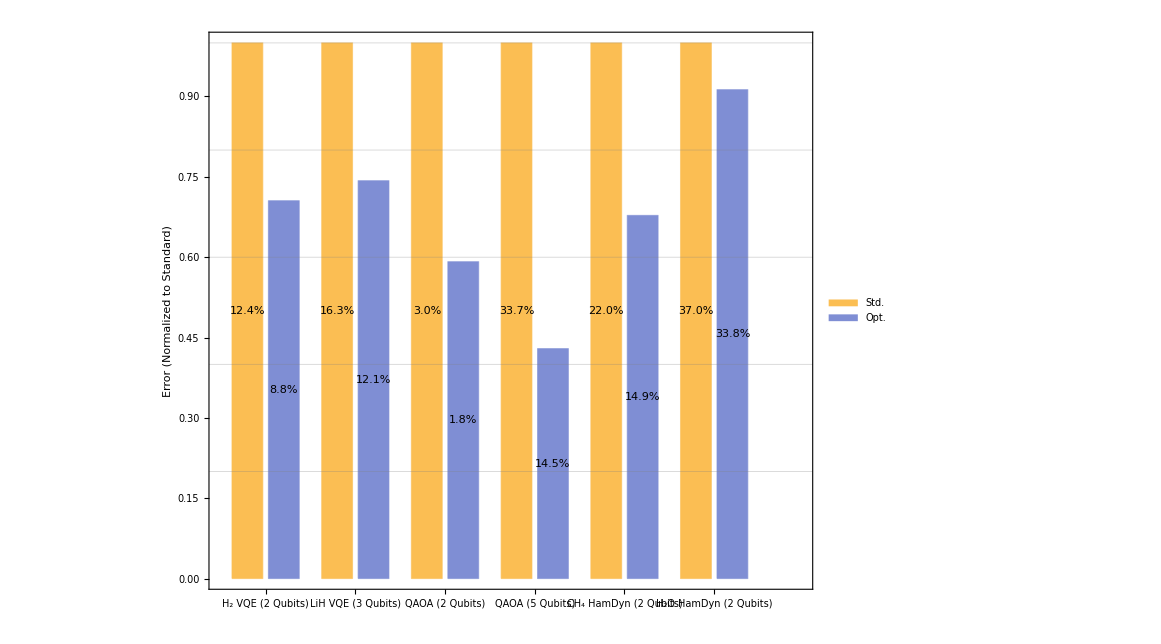

```mathematica
BarChart[{{Labeled[1,"12.4%", Center],Labeled[(1-0.9123656660760371)/(1-0.875771793985852),"8.8%", Center]},{Labeled[1,"16.3%", Center],Labeled[(1-0.8789601928909436)/(1-0.8370469293021144),"12.1%", Center]},{Labeled[1,"3.0%", Center],Labeled[(1-0.9821760223952822)/(1-0.9698696167697216),"1.8%", Center]},
{Labeled[1,"33.7%", Center],Labeled[(1-0.8552290613698698)/(1-0.6627697370128571),"14.5%", Center]},
{Labeled[1,"22.0%", Center],Labeled[(1-0.8511686649454064)/(1-0.7804729339827983),"14.9%", Center]},
{Labeled[1,"37.0%", Center],Labeled[(1-0.6620373759074387)/(1-0.6297207853684704),"33.8%", Center]},
{}
},ChartLegends->Placed[{"Std.","Opt."}, {0.9, 0.95}], ChartLabels->{{"H₂ VQE\n(2 Qubits)", "LiH VQE\n(3 Qubits)", "QAOA\n(2 Qubits)", "QAOA\n(5 Qubits)", "CH_4 HamDyn\n(2 Qubits)", "H₂O HamDyn\n(2 Qubits)", ""},None},
BaseStyle->{FontSize->16},LabelStyle->Black,
AspectRatio->.75,
GridLines->{{}, {0.2, 0.4, 0.6, 0.8, 1.0}},
Axes->False,Frame->True,FrameLabel->{None,Style["  Error (Normalized to Standard)",24]}]
```

```mathematica
BarChart[
{{Labeled[(1-0.875771793985852)/(1-0.9123656660760371),HoldForm[(("12.4%")/("8.8%"))], Center] },
{Labeled[(1-0.8370469293021144)/(1-0.8789601928909436),HoldForm[(("16.3%")/("12.1%"))], Center]},
{Labeled[(1-0.9698696167697216)/(1-0.9821760223952822),HoldForm[(("3.0%")/("1.8%"))], Center]},
{Labeled[(1-0.6627697370128571)/(1-0.8552290613698698),HoldForm[(("33.7%")/("14.5%"))], Center]},
{Labeled[(1-0.7804729339827983)/(1-0.8511686649454064),HoldForm[(("22.0%")/("14.9%"))], Center]},
{Labeled[(1-0.6297207853684704)/(1-0.6620373759074387),HoldForm[(("37.0%")/("33.8%"))], Center]},
},
ChartLabels->{{"H₂ VQE\n(2 Qubits)", "LiH VQE\n(3 Qubits)", "QAOA\n(2 Qubits)", "QAOA\n(5 Qubits)", "CH_4 HamDyn\n(2 Qubits)", "H₂O HamDyn\n(2 Qubits)"},None},
Axes->False,Frame->True,FrameLabel->{None,Style["Error Reduction  (Standard/Optimized)",24]},
BaseStyle->{FontSize->17},LabelStyle->Black,
GridLines->{{}, {0.5, 1.0, 1.5, 2.0, 2.5}},
AspectRatio->.8]
```